## Normal Way

```mathematica
ψ[n_,x_]:=Subscript[A, n] x^n Exp[-α/2 x^2]
(*Subscript[A, n_]:=α^(1/4+n/2)/(√Gamma[1/2+n])*)
```

### Find Normalization Factor

```mathematica
Assuming[{n≥0&&n∈Integers,α>0},∫_(-∞)^∞ ψ[n,x]^2 ⅆx]==1
Solve[%,Subscript[A, n]]
```

α^(-1/2-n) Gamma[1/2+n] A_n^2==1

{{A_n→-α^(1/2 (1/2+n))/(√Gamma[1/2+n])},{A_n→α^(1/2 (1/2+n))/(√Gamma[1/2+n])}}

```mathematica
Subscript[A, n_]:=α^(1/4+n/2)/(√Gamma[1/2+n])
```

### Show ⟨x⟩==⟨p⟩==0

```mathematica
x1=Assuming[{n≥0&&n∈Integers,α>0},∫_(-∞)^∞ ψ[n,x]x ψ[n,x]ⅆx]
```

0

```mathematica
Assuming[{n≥0&&n∈Integers,α>0},-ⅈ ℏ∫_(-∞)^∞ ψ[n,x]D[ψ[n,x], x]ⅆx]
p1=Refine[%,n>0]
```

ConditionalExpression[0,n>0]

0

### Calculate ⟨x^2⟩ and ⟨p^2⟩

```mathematica
x2=Refine[∫_(-∞)^∞ ψ[n,x]^2 x^2 ⅆx,{n∈Integers&&n≥0,α>0}]//FullSimplify
```

(1+2 n)/(2 α)

```mathematica
p2=Refine[-ℏ^2∫_(-∞)^∞ ψ[n,x]D[ψ[n,x], x,x]ⅆx,{n∈Integers&&n≥0,α>0}]//FullSimplify
```

ConditionalExpression[((-1+4 n) α ℏ^2)/(-2+4 n),n>1/2]

```mathematica
p2=((-1+4 n) α ℏ^2)/(-2+4 n)
```

((-1+4 n) α ℏ^2)/(-2+4 n)

### ΔA==√(,⟨A^2⟩-⟨A⟩^2)

```mathematica
Δx=√(x2-x1^2)
```

(√((1+2 n)/α))/(√2)

```mathematica
Δp=√(p2-p1^2)
```

√(((-1+4 n) α ℏ^2)/(-2+4 n))

### Plot ΔxΔp against h/(4π)

#### But first, some simplification

```mathematica
Refine[Δp Δx,{α>0,n≥0&&n∈Integers,ℏ>0}]
```

(√(1+2 n) √((-1+4 n)/(-2+4 n)) ℏ)/(√2)

Simplifies to

Simplifies to

```mathematica
ℏ √((8 n^2+2n-1)/(8n-4))
```

#### Uncertainty Principle

```mathematica
√((8 n^2+2n-1)/(8n-4))≥1/2
```

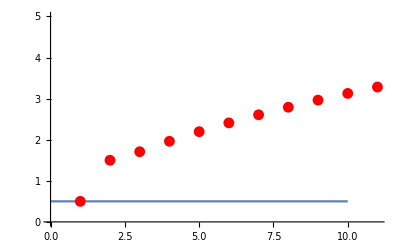

```mathematica
T1=Table[√((8 n^2+2n-1)/(8n-4)),{n,0,10}];
Show[Plot[1/2,{n,0,10}],ListPlot[T1,PlotStyle->Red],PlotRange->{0,5}]
```

## Shorter Way

```mathematica
ψ[n_,x_]:=Subscript[A, n] x^n Exp[-1/2 α x^2]
```

Lets define an auxiliary function ϕ, which is the gaussian function

```mathematica
ϕ[x_]:=Exp[-1/2 α x^2]
```

Successive derivatives of ϕ with respect to α give ψ (unnormalized of course)

```mathematica
Table[
{(-1)^n 2^n Subscript[A, n] D[ϕ[x],{α,n}],ψ[n,x]},
{n,0,10}
]//TableForm
```

ⅇ^(-(x^2 α)/2) A_0 | ⅇ^(-(x^2 α)/2) A_0
ⅇ^(-(x^2 α)/2) x^2 A_1 | ⅇ^(-(x^2 α)/2) x A_1
ⅇ^(-(x^2 α)/2) x^4 A_2 | ⅇ^(-(x^2 α)/2) x^2 A_2
ⅇ^(-(x^2 α)/2) x^6 A_3 | ⅇ^(-(x^2 α)/2) x^3 A_3
ⅇ^(-(x^2 α)/2) x^8 A_4 | ⅇ^(-(x^2 α)/2) x^4 A_4
ⅇ^(-(x^2 α)/2) x^10 A_5 | ⅇ^(-(x^2 α)/2) x^5 A_5
ⅇ^(-(x^2 α)/2) x^12 A_6 | ⅇ^(-(x^2 α)/2) x^6 A_6
ⅇ^(-(x^2 α)/2) x^14 A_7 | ⅇ^(-(x^2 α)/2) x^7 A_7
ⅇ^(-(x^2 α)/2) x^16 A_8 | ⅇ^(-(x^2 α)/2) x^8 A_8
ⅇ^(-(x^2 α)/2) x^18 A_9 | ⅇ^(-(x^2 α)/2) x^9 A_9
ⅇ^(-(x^2 α)/2) x^20 A_10 | ⅇ^(-(x^2 α)/2) x^10 A_10